```mathematica
f[x_]=exp(x-(x/4)^2)*th((x/11)^3+1/3);
```

```mathematica
a=0;b=6;n=6;h=(b-a)/n;
```

```mathematica
data=N[Table[{a+i*h,f[a+i*h]},{i,0,n}]]
```

{{0.,0.},{1.,6.62449},{2.,6.28882},{3.,3.90999},{4.,2.38627},{5.,2.29086},{6.,3.03234}}

```mathematica
TableForm[data]
```

0. | 0.
1. | 6.62449
2. | 6.28882
3. | 3.90999
4. | 2.38627
5. | 2.29086
6. | 3.03234

```mathematica
Pr[x_]=∏_(i=0)^n (x-(a+b)/n*i);
```

```mathematica
DPr[x_]=D[Pr[x],x];
```

```mathematica
t[x_]=∑_(i=0)^n f[(a+b)/n*i]*Pr[x]/((x-(a+b)/n*i)*DPr[(a+b)/n*i])//N;
```

```mathematica
Expand[t[x]]
```

11.9425 x-6.17804 x^2+0.776496 x^3+0.114566 x^4-0.0331094 x^5+0.00203712 x^6

```mathematica
gr1=Plot[f[x],{x,0,6}];
```

```mathematica
gr2=Plot[t[x],{x,0,6},PlotStyle-> {Green,Thickness[0.0056]}];
```

```mathematica
gr3=ListPlot[data,PlotStyle->PointSize[0.015]];
```

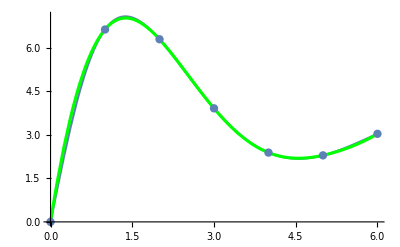

```mathematica
Show[gr1,gr2,gr3]
```

```mathematica
Array[dif,{n+1,n+1},{0,0}];
```

```mathematica
For[k=1,k≤n,k++,
For[i=n,i≥n-k,i--,dif[i,k]=""]];
```

```mathematica
For[i=0,i≤n,i++,dif[i,0]=data[[i+1,2]]];
```

```mathematica
For[k=1,k≤n,k++,
For[i=0,i≤n-k,i++,
dif[i,k]=dif[i+1,k-1]-dif[i,k-1]]];
```

```mathematica
tab=Array[dif,{n+1,n+1},{0,0}];
```

```mathematica
PaddedForm[TableForm[tab],{6,5}]
```

0.00000 |  6.62449 | -6.96016 |  4.91701 | -2.01875 | -0.30631 |  1.46673
 6.62449 | -0.33567 | -2.04316 |  2.89826 | -2.32505 |  1.16042 | 
 6.28882 | -2.37883 |  0.85510 |  0.57321 | -1.16463 |  | 
 3.90999 | -1.52372 |  1.42831 | -0.59142 |  |  | 
 2.38627 | -0.09541 |  0.83689 |  |  |  | 
 2.29086 |  0.74148 |  |  |  |  | 
 3.03234 |  |  |  |  |  |

```mathematica
h=(b-a)/n;
q=(x-b)/h;
Nw[x_]=dif[n,0];
qF[q_]=1;
For[i=1,i≤n,i++,
	qF[q_]=qF[q]*(q+i-1);
	Nw[q_]=Nw[q]+dif[n-i,i]/i!*qF[q];
]
Nw[x_]=Simplify[Nw[x]]
```

0.+11.9425 x-6.17804 x^2+0.776496 x^3+0.114566 x^4-0.0331094 x^5+0.00203712 x^6

```mathematica
gr1:=Plot[f[x],{x,0,5}];
```

```mathematica
gr2:=ListPlot[data,PlotStyle->PointSize[0.015]];
```

```mathematica
gr3=Plot[Nw[x],{x,0,5},PlotStyle->Red];
```

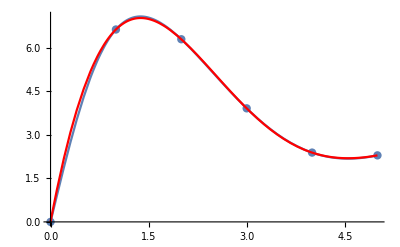

```mathematica
Show[gr1,gr2,gr3]
```

```mathematica
Np[x_]=InterpolatingPolynomial[data,x]
```

3.03234+(-6.+x) (0.50539+(-0.26598+(0.47892+(-0.0805802+(0.0015217+0.00203712 (-2.+x)) (-5.+x)) (-1.+x)) (-3.+x)) (0.+x))

```mathematica
Np[x_]=Simplify[Np[x]]
```

4.44089×10^-16+11.9425 x-6.17804 x^2+0.776496 x^3+0.114566 x^4-0.0331094 x^5+0.00203712 x^6

```mathematica
gr4:=Plot[Np[x],{x,0,5},PlotStyle->Green];
```

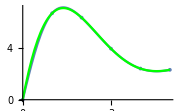

```mathematica
Show[gr1,gr2,gr4,ImageSize->Small]
```

```mathematica
f[2.4316]
```

5.26999

```mathematica
t[2.4316]
```

5.28633

```mathematica
Nw[2.4316]
```

5.28633

```mathematica
Np[2.4316]
```

5.28633

```mathematica
R[x_]:=Abs[f[x]-Np[x]];
```

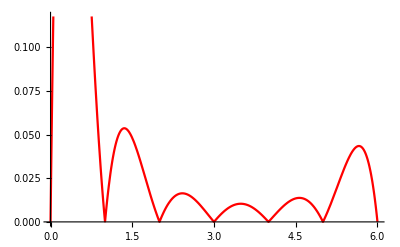

```mathematica
Plot[R[x],{x,0,6},PlotStyle->Red]
```

```mathematica
FindMaximum[R[x],{x,0,6}]
```

{0.342682,{x→0.310191}}

```mathematica
a=0;b=6;n=10;h=(b-a)/n;
```

```mathematica
data=N[Table[{a+i*h,f[a+i*h]},{i,0,n}]]
```

{{0.,0.},{0.6,4.90438},{1.2,6.98267},{1.8,6.67339},{2.4,5.3485},{3.,3.90999},{3.6,2.82088},{4.2,2.26059},{4.8,2.21428},{5.4,2.53954},{6.,3.03234}}

```mathematica
TableForm[data]
```

0. | 0.
0.6 | 4.90438
1.2 | 6.98267
1.8 | 6.67339
2.4 | 5.3485
3. | 3.90999
3.6 | 2.82088
4.2 | 2.26059
4.8 | 2.21428
5.4 | 2.53954
6. | 3.03234

```mathematica
Pr[x_]=∏_(i=0)^n (x-(a+b)/n*i);
```

```mathematica
DPr[x_]=D[Pr[x],x];
```

```mathematica
t[x_]=∑_(i=0)^n f[(a+b)/n*i]*Pr[x]/((x-(a+b)/n*i)*DPr[(a+b)/n*i])//N;
```

```mathematica
Expand[t[x]]
```

8.70363 x+3.31296 x^2-10.6292 x^3+7.66745 x^4-3.124 x^5+0.823541 x^6-0.143155 x^7+0.0158615 x^8-0.00101624 x^9+0.0000286744 x^10

```mathematica
gr1=Plot[f[x],{x,0,6}];
```

```mathematica
gr2=Plot[t[x],{x,0,6},PlotStyle-> {Green,Thickness[0.0056]}];
```

```mathematica
gr3=ListPlot[data,PlotStyle->PointSize[0.015]];
```

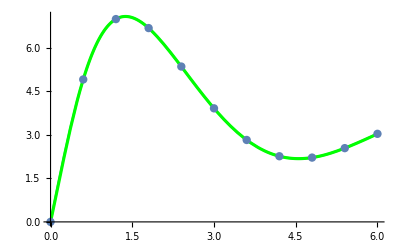

```mathematica
Show[gr1,gr2,gr3]
```

```mathematica
Array[dif,{n+1,n+1},{0,0}];
```

```mathematica
For[k=1,k≤n,k++,
For[i=n,i≥n-k,i--,dif[i,k]=""]];
```

```mathematica
For[i=0,i≤n,i++,dif[i,0]=data[[i+1,2]]];
```

```mathematica
For[k=1,k≤n,k++,
For[i=0,i≤n-k,i++,
dif[i,k]=dif[i+1,k-1]-dif[i,k-1]]];
```

```mathematica
tab=Array[dif,{n+1,n+1},{0,0}];
```

```mathematica
PaddedForm[TableForm[tab],{2,5}]
```

0.00000 |  4.90000 | -2.80000 |  0.44000 |  0.93000 | -1.40000 |  1.40000 | -1.30000 |  1.10000 | -0.89000 |  0.63000
 4.90000 |  2.10000 | -2.40000 |  1.40000 | -0.47000 |  0.03100 |  0.12000 | -0.19000 |  0.23000 | -0.26000 | 
 7.00000 | -0.31000 | -1.00000 |  0.90000 | -0.44000 |  0.16000 | -0.06600 |  0.04400 | -0.02200 |  | 
 6.70000 | -1.30000 | -0.11000 |  0.46000 | -0.28000 |  0.08900 | -0.02300 |  0.02200 |  |  | 
 5.30000 | -1.40000 |  0.35000 |  0.18000 | -0.19000 |  0.06700 | -0.00080 |  |  |  | 
 3.90000 | -1.10000 |  0.53000 | -0.01500 | -0.13000 |  0.06600 |  |  |  |  | 
 2.80000 | -0.56000 |  0.51000 | -0.14000 | -0.06200 |  |  |  |  |  | 
 2.30000 | -0.04600 |  0.37000 | -0.20000 |  |  |  |  |  |  | 
 2.20000 |  0.33000 |  0.17000 |  |  |  |  |  |  |  | 
 2.50000 |  0.49000 |  |  |  |  |  |  |  |  | 
 3.00000 |  |  |  |  |  |  |  |  |  |

```mathematica
h=(b-a)/n;
q=(x-b)/h;
Nw[x_]=dif[n,0];
qF[q_]=1;
For[i=1,i≤n,i++,
	qF[q_]=qF[q]*(q+i-1);
	Nw[q_]=Nw[q]+dif[n-i,i]/i!*qF[q];
]
Nw[x_]=Simplify[Nw[x]]
```

4.44089×10^-15+8.70363 x+3.31296 x^2-10.6292 x^3+7.66745 x^4-3.124 x^5+0.823541 x^6-0.143155 x^7+0.0158615 x^8-0.00101624 x^9+0.0000286744 x^10

```mathematica
gr1:=Plot[f[x],{x,0,5}];
```

```mathematica
gr2:=ListPlot[data,PlotStyle->PointSize[0.015]];
```

```mathematica
gr3=Plot[Nw[x],{x,0,5},PlotStyle->Red];
```

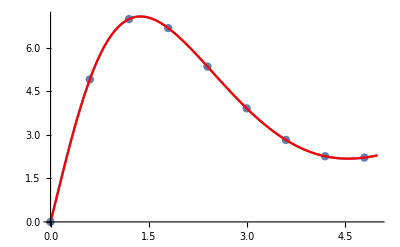

```mathematica
Show[gr1,gr2,gr3]
```

```mathematica
Np[x_]=InterpolatingPolynomial[data,x]
```

3.03234+(-6.+x) (0.50539+(-0.26598+(0.467222+(-0.0830686+(0.00669431+(0.00438551+(-0.00203813+(0.000489592+(-0.000173214+0.0000286744 (-1.8+x)) (-4.2+x)) (-2.4+x)) (-0.6+x)) (-5.4+x)) (-4.8+x)) (-1.2+x)) (-3.+x)) (0.+x))

```mathematica
Np[x_]=Simplify[Np[x]]
```

4.44089×10^-16+8.70363 x+3.31296 x^2-10.6292 x^3+7.66745 x^4-3.124 x^5+0.823541 x^6-0.143155 x^7+0.0158615 x^8-0.00101624 x^9+0.0000286744 x^10

```mathematica
gr4:=Plot[Np[x],{x,0,5},PlotStyle->Green];
```

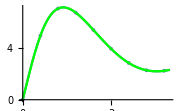

```mathematica
Show[gr1,gr2,gr4,ImageSize->Small]
```

```mathematica
f[2.4316]
```

5.26999

```mathematica
t[2.4316]
```

5.26999

```mathematica
Nw[2.4316]
```

5.26999

```mathematica
Np[2.4316]
```

5.26999

```mathematica
R[x_]:=Abs[f[x]-Np[x]];
```

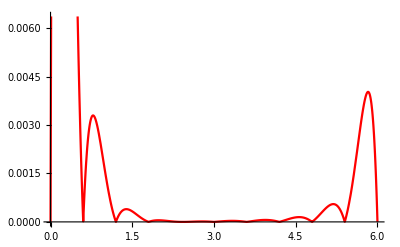

```mathematica
Plot[R[x],{x,0,6},PlotStyle->Red]
```

```mathematica
FindMaximum[R[x],{x,0,6}]
```

{0.0405509,{x→0.159605}}